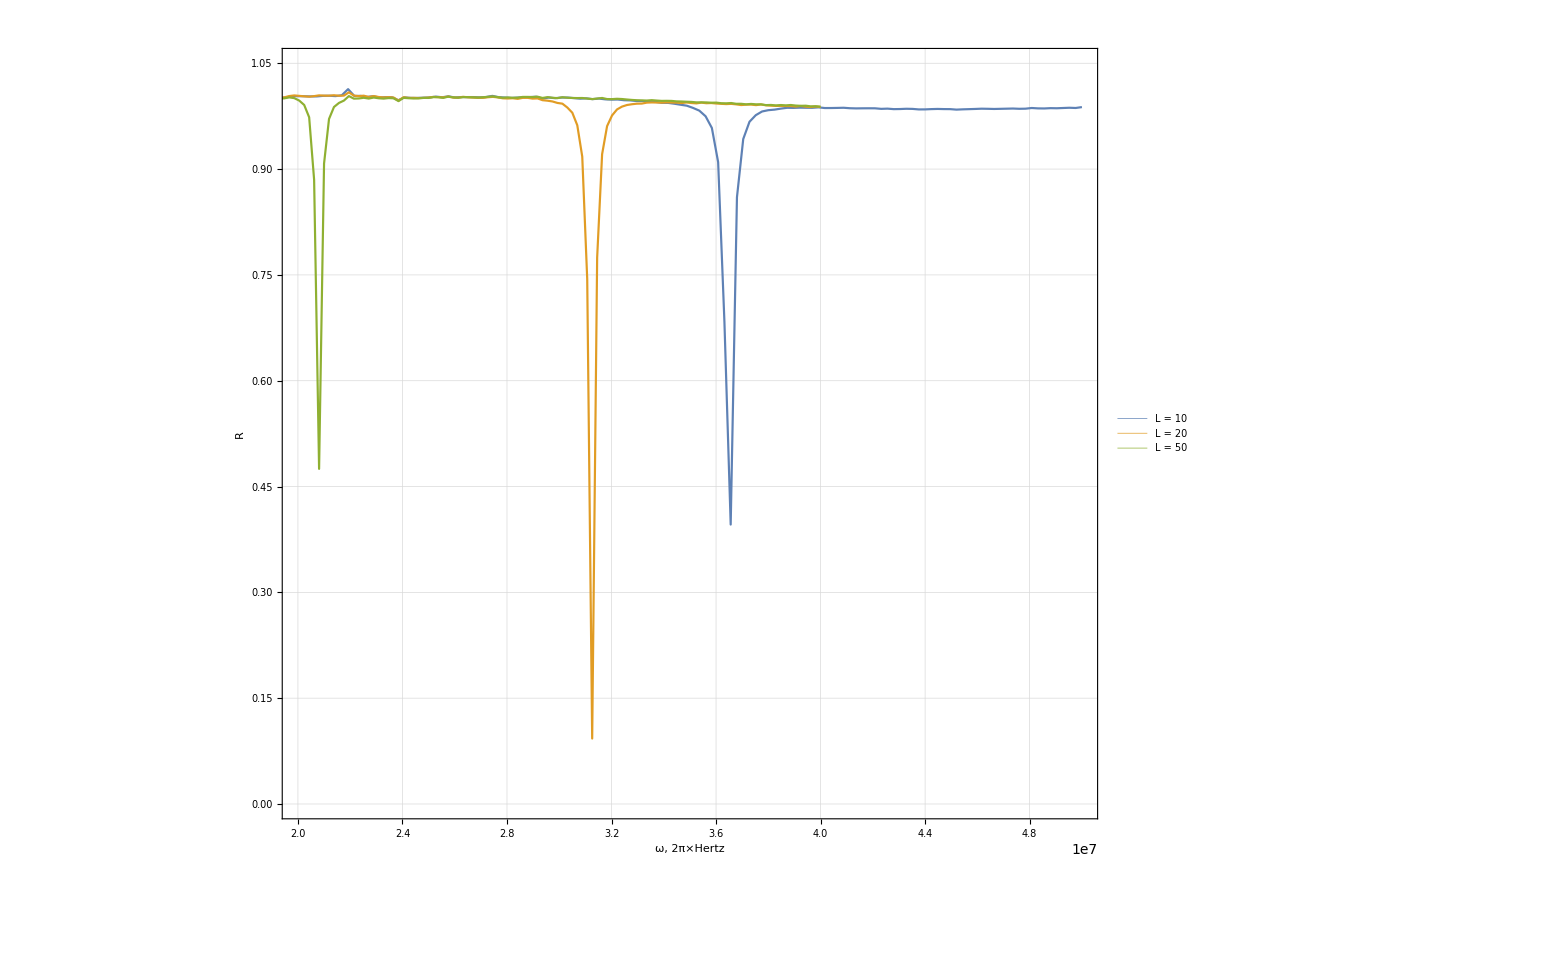

```mathematica
SetDirectory[NotebookDirectory[]];
Import[#][[19;;-2]]&/@{"QQ9.csv", "QQ4.csv","QQ5.csv"};
ListLinePlot[%, 
PlotRange->{{2*10^7,5*10^7},{0, 1.05}},
PlotLegends->Placed[
{{"L = 10", "L = 20", "L = 50"}},
{0.08,0.15}
],
PlotTheme->"Detailed",
PlotStyle->Thickness[0.001],
FrameLabel->{Style["ω, 2π×Hertz", 17], Style["R", 17]},
FrameStyle->Directive[Black, 15],
ImageSize->Large
]
(*Export["../images/R_plot_C_22.png",%, ImageResolution->500]*)
```

```mathematica
height = 0.47631;
omega = 2.08;
left=2.07144;
right=2.08573;
1-(1-height)/√2
omega/Abs[left-right]
```

0.629695

145.556

{Simulations,C_load = 10; L_coax = 10,C_load = 10; L_coax = 20,C_load = 10; L_coax = 50,C_load = 15; L_coax = 10,C_load = 15; L_coax = 20,C_load = 15; L_coax = 50,C_load = 22; L_coax = 10,C_load = 22; L_coax = 20,C_load = 22; L_coax = 50}

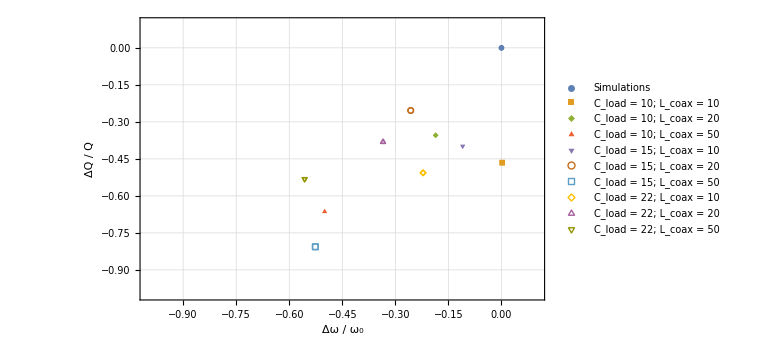

../images/Q_w_plot.png

```mathematica
val10 = {{44.7, 223.5},{36.3, 269.9}, {22.3, 140.4}};
val15 = {{40.6, 216.5}, {33.9, 268.6}, {21.6, 69.7}};
val22 = {{36.5,153.5}, {31.2, 192.3}, {20.8, 145.6}};
center[ w_,Q_]:={(First@#-w)/w, (Last@# - Q)/Q}&
val10 = center[44.6,418]/@val10;
val15 = center[45.6,360]/@val15;
val22 = center[46.9,311]/@val22;

legends = Table[
StringTemplate["C_load = ``; L_coax = ``"][capacitance, length],
{capacitance, {10, 15, 22}},
{length, {10, 20, 50}}
]//Flatten;
legends = Join[{"Simulations"}, legends]
legends = Style[#, 14]&/@legends;

ListPlot[{#}&/@Join[{{0, 0}}, val10, val15, val22],
PlotRange->{{-1,0.1},{-1, 0.1}},
PlotLegends->Placed[
{legends},
{0.17,0.5}
],
PlotMarkers->{Automatic, Large},
PlotTheme->"Detailed",
FrameLabel->{Style["Δω / ω_0", 17], Style["ΔQ / Q", 17]},
FrameStyle->Directive[Black, 15],
ImageSize->Large
]
Export["../images/Q_w_plot.png",%, ImageResolution->500]
```

```mathematica
data = {
{10*10^-12, (2π*44.7*10^6)^-2}, 
{15*10^-12, (2π*40.6*10^6)^-2}, 
{22*10^-12, (2π*36.5*10^6)^-2}
};
fit10=FindFit[data,Lres*(Cres + dC),{{Lres, 4.5*10^-7}, {Cres,10^-12}},dC];
data = {
{10*10^-12, (2π*36.3*10^6)^-2}, 
{15*10^-12, (2π*33.9*10^6)^-2}, 
{22*10^-12, (2π*21.6*10^6)^-2}
};
fit15=FindFit[data,Lres*(Cres + dC),{{Lres, 4.5*10^-7}, {Cres,10^-12}},dC];
data = {
{10*10^-12, (2π*22.3*10^6)^-2}, 
{15*10^-12, (2π*21.6*10^6)^-2}, 
{22*10^-12, (2π*20.8*10^6)^-2}
};
fit22=FindFit[data,Lres*(Cres + dC),{{Lres, 4.5*10^-7}, {Cres,10^-12}},dC];
Lres =(Lres/.#)&/@{fit10, fit15, fit22}//Mean
U0 = 300;
w0 = ;
Qres = ;
```

6.06921×10^-7